# Определение микропараметров I_2 с помощью спектрометра

### Подгрузка предыдущих результатов (Calculations.nb)

Важно : в данном расчете убрана одна серия

Параметры калибровки

```mathematica
(*Initialization*)
CalibrationHg=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\I2 Data Processing\\Calibration_Hg.xlsx"][[1]][[2;;All,1;;2]];
calibWaveLengths=CalibrationHg[[All,1]];
calibPixel=CalibrationHg[[All,2]];
calibrationHgReady=Transpose[ArrayReshape[AppendTo[calibPixel,calibWaveLengths],{2,Length[calibWaveLengths]}]];
fit=FindFit[calibrationHgReady,{a+c/(x-b),b<0},{a,b,c},x]
Calibrate[λ_]:=a+c/(λ-b)/.fit;
```

{a→2889.97,b→-4060.89,c→1.42866×10^7}

Откалиброванный спектр с выделенными пиками

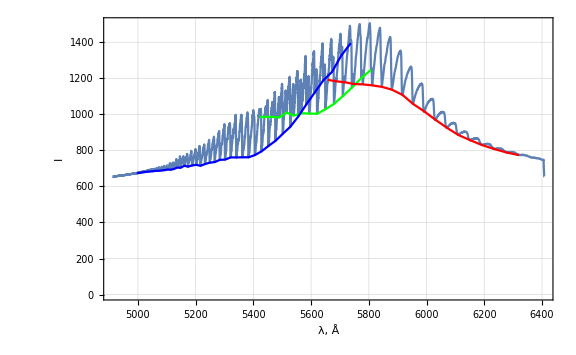

```mathematica
i2Spectre=ReadList["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\26_11_2018\\i2-clear.txt",Number,WordSeparators->{"\t", "\n"}];
i2Spectre=ArrayReshape[i2Spectre,{Length[i2Spectre]/5,5}];
peaksStorage=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\I2 Data Processing\\peaksStorage_short.xlsx"];
seriesPlots={};
For[i=1,i≤Length[peaksStorage],i++,
AppendTo[seriesPlots,ListLinePlot[Transpose[peaksStorage[[i]]],PlotStyle->Hue[i/Length[peaksStorage]]]]
]
calibratedI2Spectre=Transpose[{Calibrate[i2Spectre[[All,1]]],i2Spectre[[All,2]],i2Spectre[[All,3]],i2Spectre[[All,4]],i2Spectre[[All,5]]}];
calibratedPeaksStorage={};
For[i=1,i≤ Length[peaksStorage],i++,
AppendTo[calibratedPeaksStorage,{Calibrate[peaksStorage[[i]][[1]]],peaksStorage[[i]][[2]]}]
]
calibratedSeriesPlots={};
For[i=1,i≤Length[calibratedPeaksStorage],i++,
AppendTo[calibratedSeriesPlots,ListLinePlot[Transpose[calibratedPeaksStorage[[i]]],PlotStyle->Hue[i/Length[calibratedPeaksStorage]]]]
]
Show[ListLinePlot[Transpose[{calibratedI2Spectre[[All,1]],calibratedI2Spectre[[All,3]]}],PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"λ, Å","I"}],calibratedSeriesPlots]
```

График зависимости энергии пика в серии от номера пика

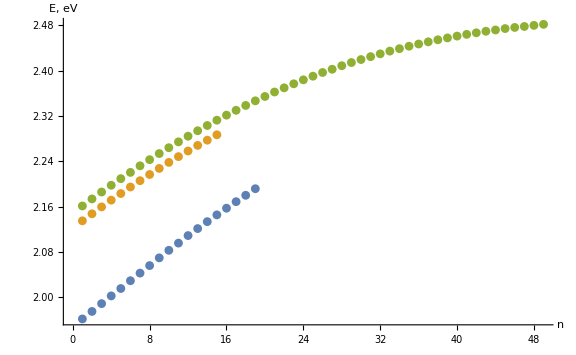

```mathematica
energyPeaks={};
For[i=1,i≤ Length[calibratedPeaksStorage],i++,
AppendTo[energyPeaks,UnitConvert[(h c)/Quantity[calibratedPeaksStorage[[i,1]],"Angstroms"]/.{h-> Quantity[1,"PlanckConstant"],c-> Quantity[1,"SpeedOfLight"]},"Electronvolts"]]
]
energyPeaks=QuantityMagnitude[energyPeaks];
energyPeaks=SortBy[energyPeaks,First];
energyPeaksNumerated={};
series={};
For[i=1,i≤ Length[energyPeaks],i++,
For[j=1,j≤ Length[energyPeaks[[i]]],j++,
AppendTo[series,{j,energyPeaks[[i,j]]}];
];
AppendTo[energyPeaksNumerated,series];
series={};
]
ListPlot[energyPeaksNumerated,AxesLabel->{"n","E, eV"}]
```

График зависимости энергии пика в серии от номера пика с подобранными дискретными значенями сдвигов

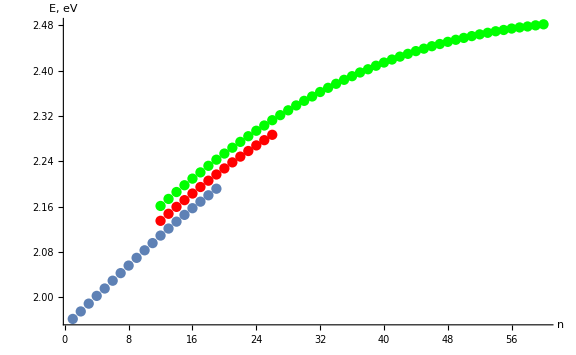

```mathematica
offsets={0,11,11};
o1=offsets[[1]];
o2=offsets[[2]];
o3=offsets[[3]];
Show[
ListPlot[energyPeaksNumerated[[1]]+Table[{o1,0},Length[energyPeaksNumerated[[1]]]],AxesLabel->{"n","E, eV"},ImageSize->Large],
ListPlot[energyPeaksNumerated[[2]]+Table[{o2,0},Length[energyPeaksNumerated[[2]]]],PlotStyle->Red],
ListPlot[energyPeaksNumerated[[3]]+Table[{o3,0},Length[energyPeaksNumerated[[3]]]],PlotStyle->Green],
PlotRange->All
]
```

График зависимостей разностей энергий между сериями

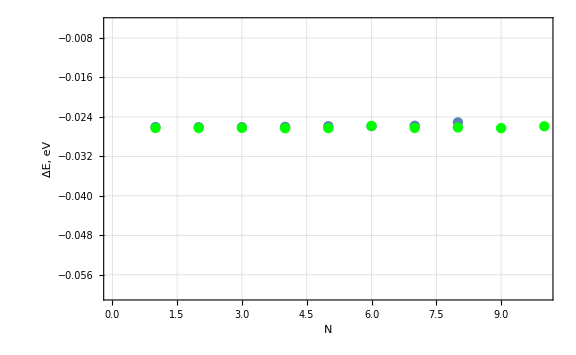

```mathematica
DeltaS1 = energyPeaks[[1, Max[o1, o2] - o1 + 1 ;; Max[o1, o2] - o1 + 1 + Min[Length[energyPeaks[[1]]] - (Max[o1, o2] - o1 + 1), Length[energyPeaks[[2]]] - (Max[o1, o2] - o2 + 1)]]] -
      energyPeaks[[2, Max[o1, o2] - o2 + 1 ;; Max[o1, o2] - o2 + 1 + Min[Length[energyPeaks[[1]]] - (Max[o1, o2] - o1 + 1), Length[energyPeaks[[2]]] - (Max[o1, o2] - o2 + 1)]]];
DeltaS2 = energyPeaks[[2, Max[o2, o3] - o2 + 1 ;; Max[o2, o3] - o2 + 1 + Min[Length[energyPeaks[[2]]] - (Max[o2, o3] - o2 + 1), Length[energyPeaks[[3]]] - (Max[o2, o3] - o3 + 1)]]] -
      energyPeaks[[3, Max[o2, o3] - o3 + 1 ;; Max[o2, o3] - o3 + 1 + Min[Length[energyPeaks[[2]]] - (Max[o2, o3] - o2 + 1), Length[energyPeaks[[3]]] - (Max[o2, o3] - o3 + 1)]]];
Show[
ListPlot[
DeltaS1,ImageSize->Large,PlotTheme->"Detailed"
],
ListPlot[
DeltaS2,PlotStyle->Green,ImageSize->Large
],PlotRange->{{0,10},{-0.06,-0.005}},FrameLabel->{"N", "ΔE, eV"}
]
```

Вычислим тангенсы угла наклона графиков ΔE (n) как коэффициент при переменной в линейной функции, котрую найдем из МНК

```mathematica
LinearModelFit[DeltaS1,x,x]["BestFitParameters"][[2]]
LinearModelFit[DeltaS2,x,x]["BestFitParameters"][[2]]
```

0.000105947

0.0000299735

Рассчитаем среднее значение сдвига энергии ΔE

```mathematica
AverageDE=Abs[Mean[{Mean[DeltaS1],Mean[DeltaS2]}]]
```

0.0259718

Построим график итоговой зависимости ΔE (n) с учетом среднего значения сдвига

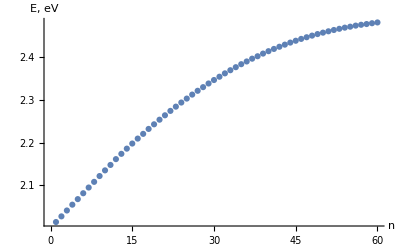

```mathematica
fullPeaks=Join[energyPeaks[[1]][[1;;11]]+2*AverageDE,energyPeaks[[3]]];
ListPlot[fullPeaks,AxesLabel->{"n","E, eV"}]
```

### Экстраполяция

Выражение для энергетического спектра движения в потенциале Морзе имеет вид:

ⅇ_n=(n+1/2) ℏα √((2 A)/μ)-A+d-((n+1/2)^2 (α^2 ℏ^2))/(2 μ)

Найдем параметры кривой для полученного ранее набора точек, предварительно задав несколько констант.

```mathematica
ℏ=QuantityMagnitude[UnitConvert[(Quantity[1,"PlanckConstant"]/(2π)),"Electronvolts"*"Seconds"]]
```

6.58212×10^-16

```mathematica
μ=QuantityMagnitude[UnitConvert[ElementData["Iodine","AtomicMass"]/2*Quantity[1,"SpeedOfLight"]^2,"Electronvolts"]]
```

5.910538×10^10

Найдем параметры d и A

```mathematica
fitEquation=Fit[fullPeaks,{1,x,x^2},x]
k=CoefficientList[fitEquation,x]
params=CoefficientList[Expand[(n+1/2)*ℏ*α*√((2A)/μ)-A+d-((n+1/2)^2(α^2 ℏ^2))/(2μ)],n]
MorseFit=Solve[{params[[1]]==k[[1]],params[[2]]==k[[2]],params[[3]]==k[[3]]},{d,A,α}]
```

1.99499+0.0153127 x-0.000120732 x^2

{1.99499,0.0153127,-0.000120732}

{-A+d+1.91442×10^-21 √A α-9.16251×10^-43 α^2,3.82884×10^-21 √A α-3.665×10^-42 α^2,-3.665×10^-42 α^2}

{{d→2.48053,A→0.493226,α→5.7395×10^18}}

Построим энергетический спектр движения

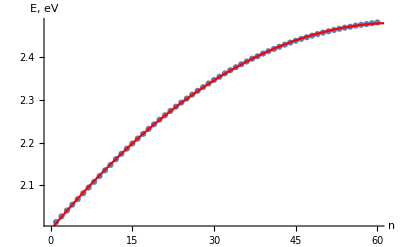

```mathematica
Show[
ListPlot[fullPeaks],
Plot[(n+1/2)*ℏ*α*√((2A)/μ)-A+d-((n+1/2)^2(α^2 ℏ^2))/(2μ)/.MorseFit,{n,0,78},PlotStyle->Red],AxesLabel->{"n","E, eV"}
]
```

### Построение потенциала Морзе

Выражение для потенциала Морзе имеет вид

```mathematica
U^eff(ρ)=A(ⅇ^(-2α(ρ-Subscript[ρ, 0]))-2 ⅇ^(-α(ρ-Subscript[ρ, 0])))+d
```

В рамках экперимента мы не можем определить ρ_0, поэтому возьмем табличную величину ρ_0=3.024Å

Для начала сведем в систему СИ величины μ и ℏ, а α выразим в 1/Å:

```mathematica
μ = UnitConvert[ElementData["Iodine", "AtomicMass"]]/2
ℏ=UnitConvert[Quantity[1,"PlanckConstant"]]/(2π)
αs=UnitConvert[√((-Quantity[k[[3]],"Electronvolts"]*2μ)/ℏ^2),1/"Angstroms"]
```

1.053649×10^-25 kg

1.054572×10^-34 kg m^2/s

1.91449 /Å

Построим график потенциала Морзе вместе с энергетическими уровнями стационарных состояний для возбужденного терма.

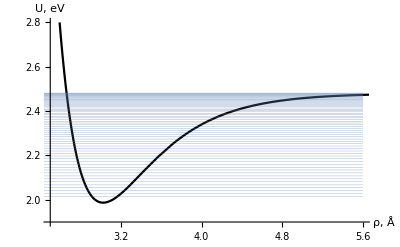

```mathematica
ρ0=3.024;
αs=QuantityMagnitude[αs];
Ueff[ρ_]:=(A(E^(-2αs(ρ-ρ0))-2 E^(-αs(ρ-ρ0)))+d);
lvls={};
For[i=1,i≤60,i++,
AppendTo[lvls,Plot[fullPeaks[[i]],{x,0,5.6},PlotStyle->Thickness[0.0005](*,PlotStyle-> Hue[i/78]*)]];
]
ePlot=Show[Plot[Ueff[ρ]/.MorseFit,{ρ,0,7},PlotStyle->Black,PlotRange->{{2.5,5.6},{1.9,2.8}},AxesLabel->{"ρ, Å","U, eV"}],lvls,PlotTheme->"Detailed"]
```

Теперь построим график, на котором будет отображен основной терм.

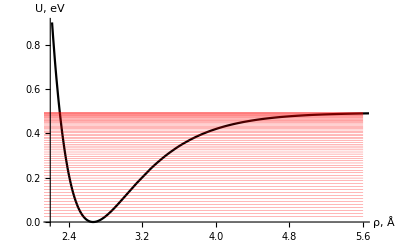

```mathematica
ρ1=2.666;
Ueff1[ρ_]:=(A(E^(-2αs(ρ-ρ1))-2 E^(-αs(ρ-ρ1)))+A);
lvls2={};
For[i=1,i≤60,i++,
AppendTo[lvls2,Plot[fullPeaks[[i]]-(d-A)/.MorseFit,{x,0,5.6},PlotStyle->{Thickness[0.0005],Red}(*,PlotStyle-> Hue[i/78]*)]];
]
mPlot=Show[Plot[Ueff1[ρ]/.MorseFit,{ρ,0,7},PlotStyle->Black,PlotRange->{{2.2,5.6},{0,0.9}},AxesLabel->{"ρ, Å","U, eV"}],lvls2,PlotTheme->"Detailed"]
```

Сведем оба графика

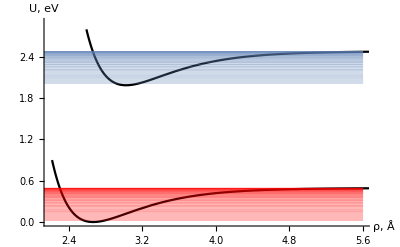

```mathematica
Show[ePlot,mPlot,PlotRange->{{2.2,5.6},{0,2.9}},AxesLabel->{"ρ, Å","U, eV"},AxesOrigin-> Automatic]
```

```mathematica
d-A/.MorseFit
```

{1.9873}